# Susceptibility of relaxor ferroelectrics by statistical modeling

In this document, we explore the idea of fitting the static susceptibility of BZT using Maxwell-Boltzmann distribution.

```mathematica
SetOptions[Plot,BaseStyle->FontSize->12];
SetOptions[Plot,AxesStyle->Directive[Black,21,FontFamily->"Times New Roman"],LabelStyle->Directive[Black,FontFamily->"Times New Roman"]];
SetOptions[ListPlot,AxesStyle->Directive[Black,21,FontFamily->"Times New Roman"],LabelStyle->Directive[Black,FontFamily->"Times New Roman"]];SetOptions[ListPlot,BaseStyle->FontSize->12];
```

## Maxwell-Boltzmann distribution

As we know, the Maxwell-Boltzmann distribution is used to describe a group of particles at a given temperature. 

For a system at temperature T, this ditribution with respect to the kinetic energy E is given by

f_E(E)=2√E/π(1/kT)^(3/2)exp(-E/kT),

which is definde in Mathematica as the follows

```mathematica
p[E_,T_]:=2*Sqrt[E/Pi]*Exp[-E/T]/T^(3/2) (*Maxwell energy distribution*)
```

For  T=200K, the distribution looks like

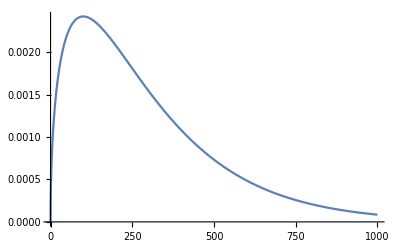

```mathematica
Plot[p[Ex,200],{Ex,0,1000}]
```

## Particles in and out of an energy well

Now we assume the system has N dipoles and an energy well of depth E_b, then the number of particles above the energy well is N× P, where P is defined as

```mathematica
P[Eb_,T_]:=(2 ⅇ^(-Eb/T) √Eb)/(√π √T)+Erfc[(√Eb)/(√T)]
```

```mathematica
Limit[P[Eb,T]/T,T->Infinity] (*Check the limit is okay*)
```

0

```mathematica
Limit[P[Eb,T],T->Infinity] (*Check the limit is okay*)
```

1

The number of particles in the energy well is obviously N×(1-P). The probality of P and (1-P) at E_b=120 K with respect to temperature is shown below.

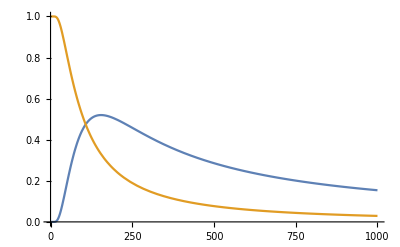

```mathematica
Plot[{P[120,T]*Tanh[160/T],(1-P[120,T])},{T,0,1000},PlotRange->All,AxesOrigin->{0,0}]
```

## Susceptibility of such a system

To obtain the susceptibility of such a system, we use a very simple assumption: particles outside of the energy well is paraelectric, whose contribution is given by the Curie law; on the other hand, particles inside the well are taken as ferroelectric, which contribute only a constant.  With this assumption, the total susceptibility is given by

χ(T)=a_1 P(E_b,T)/T+a_2[1-P(E_b,T)]

where a_1,a_2, and E_b will be fitting parameters.

## Using this equation

Now we test this equation against results obtained with MC previously.

Here is how the MC results look like

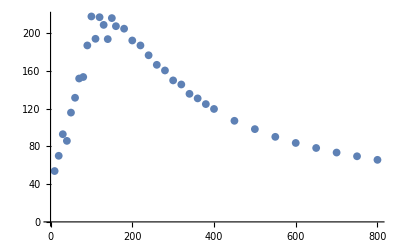

```mathematica
SetDirectory[NotebookDirectory[]];
f2=OpenRead["MC_results_2.DAT"];mc=ReadList[f2,{Number,Number}];Close[f2];(*Open MC simulation results*)
gmc=ListPlot[mc,PlotRange->All,AxesOrigin->{0,0},PlotMarkers->{Automatic,8}]
```

Here we fit the MC results, and E_b is found to be 198K.

```mathematica
langevin[x_]:=(Coth[x]-1/x)
```

```mathematica
f1[T_]:=P[Eb,T]*a1^2*3*langevin[θ/T]+(1-P[Eb,T])*a2^2
```

```mathematica
fitData[data_,model_,startingpara_]:=FindFit[data,model,startingpara,x,MaxIterations->800,Method->LevenbergMarquardt];
```

```mathematica
rslt1=fitData[mc,f1[x],{{a1,900},{Eb,159.138},{θ,150},{a2,100}}]
```

{a1→15.7224,Eb→159.138,θ→220.528,a2→8.10771}

```mathematica
g1[x_]:=(f1[x])/.rslt1
```

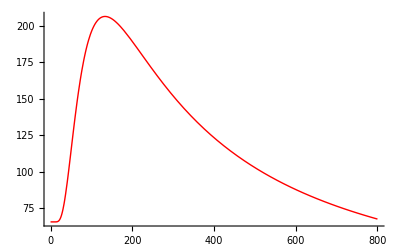

```mathematica
fmc2=Plot[{g1[x]},{x,0,800},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Thick,Red}]
```

Here is the final results, which looks quite good. But some improvement at ~0 K and at higher temperatures will be nice. Perhaps something can be done with the 1-P part.

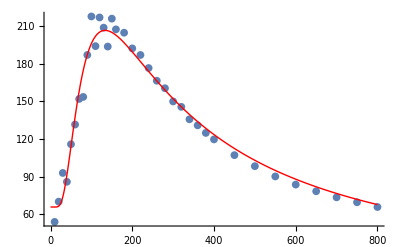

```mathematica
Fig1=Show[{gmc,fmc2},PlotRange->All]
```

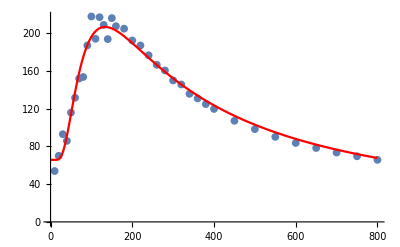
-Graphics-SusceptbilityTemperature (K)

```mathematica
fResult=Labeled[Show[gmc,fmc2],
Text/@TraditionalForm/@{Style["Susceptbility",21,Black,FontFamily->Times],Style["Temperature (K)",21,Black,FontFamily->Times],Style["",25,Black,FontFamily->Times]},{Left,Bottom,Top},Spacings->{0.2500,.0},RotateLabel->True]
```

```mathematica
Export["Fig_1_v2.pdf",fResult]
```

Fig_1_v2.pdf